# Specialized phase - Perturbative in η

```mathematica
Clear[QQ,SS,RR,r]
```

```mathematica
M=5;
```

```mathematica
K=M;
```

```mathematica
Q0=Table[Piecewise[{{1,i==j},{0,i!=j}}],{i,1,K},{j,1,K}];
```

```mathematica
R0=Table[Piecewise[{{1,i==n},{0,i!=n}}],{i,1,K},{n,1,M}];
```

```mathematica
Q=Q0+η Table[Piecewise[{{Q1,i==j},{C1,i!=j}}],{i,1,K},{j,1,K}];
R=R0+η Table[Piecewise[{{R1,i==n},{S1,i!=n}}],{i,1,K},{n,1,M}];
```

```mathematica
T=IdentityMatrix[M];
```

```mathematica
Mat=ArrayFlatten[{{Q,R},{Transpose[R],T}}];
```

```mathematica
(*Define functions based on the given equations*)J2[mat_]:=(2/Pi)*(1+mat[[1,1]]+mat[[2,2]]+mat[[1,1]] mat[[2,2]]-mat[[1,2]]^2)^(-1/2)
I3[mat_]:=(2/Pi)*(1/Sqrt[Λ3[mat]])*(mat[[2,3]] (1+mat[[1,1]])-mat[[1,2]] mat[[1,3]])/(1+mat[[1,1]])

I4[mat_]:=(4/Pi^2)*(1/Sqrt[Λ4[mat]])*ArcSin[Λ0[mat]/Sqrt[Λ1[mat] Λ2[mat]]]

(*Define auxiliary functions*)

Λ4[mat_]:=(1+mat[[1,1]]) (1+mat[[2,2]])-mat[[1,2]]^2

Λ3[mat_]:=(1+mat[[1,1]]) (1+mat[[3,3]])-mat[[1,3]]^2

Λ0[mat_]:=Λ4[mat] mat[[3,4]]-mat[[2,3]] mat[[2,4]] (1+mat[[1,1]])-mat[[1,3]] mat[[1,4]] (1+mat[[2,2]])+mat[[1,2]] mat[[1,3]] mat[[2,4]]+mat[[1,2]] mat[[1,4]] mat[[2,3]]

Λ1[mat_]:=Λ4[mat] (1+mat[[3,3]])-mat[[2,3]]^2 (1+mat[[1,1]])-mat[[1,3]]^2 (1+mat[[2,2]])+2 mat[[1,2]] mat[[1,3]] mat[[2,3]]

Λ2[mat_]:=Λ4[mat] (1+mat[[4,4]])-mat[[2,4]]^2 (1+mat[[1,1]])-mat[[1,4]]^2 (1+mat[[2,2]])+2 mat[[1,2]] mat[[1,4]] mat[[2,4]]
```

```mathematica
Nnotation[r_,indices_List]:=r^Length[DeleteDuplicates[indices]]
```

```mathematica
dR[i_,n_]:=η Sum[Nnotation[r,{i}]I3[Mat[[{i,K+n,K+m},{i,K+n,K+m}]]],{m,1,M}]-η Sum[Nnotation[r,{i,j}]I3[Mat[[{i,K+n,j},{i,K+n,j}]]],{j,1,K}]
```

```mathematica
dQ[i_,k_]:=η (Sum[Nnotation[r,{i}]I3[Mat[[{i,k,K+m},{i,k,K+m}]]],{m,1,M}]-Sum[Nnotation[r,{i,j}]I3[Mat[[{i,k,j},{i,k,j}]]],{j,1,K}])+η (Sum[Nnotation[r,{k}]I3[Mat[[{k,i,K+m},{k,i,K+m}]]],{m,1,M}]-Sum[Nnotation[r,{k,j}]I3[Mat[[{k,i,j},{k,i,j}]]],{j,1,K}])+η^2(  Sum[Sum[Nnotation[r,{i,k}]I4[Mat[[{i,k,K+m,K+n},{i,k,K+m,K+n}]]],{n,1,M}],{m,1,M}]-2   Sum[Sum[Nnotation[r,{i,k,j}]I4[Mat[[{i,k,j,K+n},{i,k,j,K+n}]]],{n,1,M}],{j,1,K}]+   Sum[Sum[Nnotation[r,{i,j,k,l}]I4[Mat[[{i,k,j,l},{i,k,j,l}]]],{j,1,K}],{l,1,K}]+Nnotation[r,{i,k}]σ^2 J2[Mat[[{i,k},{i,k}]]])
```

```mathematica
ϵg=(r^2/Pi)Sum[Sum[ArcSin[Q[[i,k]]/Sqrt[(1+Q[[i,i]])(1+Q[[k,k]])]],{i,1,K}],{k,1,K}]+(1/Pi)Sum[Sum[ArcSin[T[[n,m]]/Sqrt[(1+T[[n,n]])(1+T[[m,m]])]],{n,1,M}],{m,1,M}]-2(r/Pi)Sum[Sum[ArcSin[R[[i,n]]/Sqrt[(1+Q[[i,i]])(1+T[[n,n]])]],{i,1,K}],{n,1,M}];
```

```mathematica
eqsR=Flatten[Table[dR[i,n],{i,1,K},{n,1,M}]];
```

```mathematica
eqsQ=Flatten[Table[dQ[i,j],{i,1,K},{j,1,K}]];
```

```mathematica
eqsRexpanded=Simplify[(Normal[Series[eqsR,{η,0,2}]]-Normal[Series[eqsR,{η,0,1}]])/η^2,Assumptions->r>0];
```

```mathematica
eqsQexpanded=Simplify[(Normal[Series[eqsQ,{η,0,2}]]-Normal[Series[eqsQ,{η,0,1}]])/η^2,Assumptions->r>0];
```

```mathematica
solution=Solve[{eqsRexpanded==0,eqsQexpanded==0},{Q1,C1,S1,R1}];
```

```mathematica
ϵg2=ϵg/.solution[[1]];
```

```mathematica
ϵgf[η_,σ_,r_]=ϵg2;
```

```mathematica
r0=1;
```

```mathematica
ϵgExp=Normal[Series[ϵg,{η,0,1}]]/.solution[[1]];
```

```mathematica
f0[r_,σ_]=Coefficient[ϵgExp,η,0];
```

```mathematica
f1[r_,σ_]=Coefficient[ϵgExp,η,1];
```

```mathematica
df1[r_,σ_]=D[f1[r,σ],r];
```

```mathematica
d2f0[r_,σ_]=D[f0[r,σ],{r,2}];
```

```mathematica
r1[σ_]=-df1[r0,σ]/d2f0[r0,σ];
```

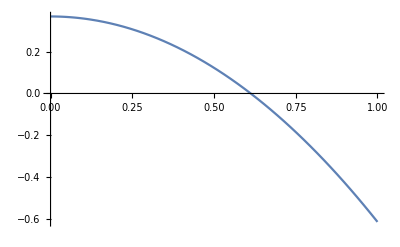

```mathematica
Plot[r1[σ],{σ,0,1}]
```